```mathematica
ClearAll["`*"]
```

```mathematica
FileMyPackages2 =HomeDirectory[]<>"/Dropbox/Study/GO/";
Needs["Go`",FileMyPackages2<>"GO2.m"];
```

Needs::nocont: Context "Go`" was not created when Needs was evaluated.

```mathematica
(*subα={GO`Private`α-> α,Abs[GO`Private`α]-> α};*)

X=Range[19];
Y=ToExpression/@ToUpperCase@ Alphabet[][[1;;19]]
subAlpha = Thread[Rule[Y,X]];
```

{A,B,C,D,ⅇ,F,G,H,ⅈ,J,K,L,M,N,O,P,Q,R,S}

-14.0874

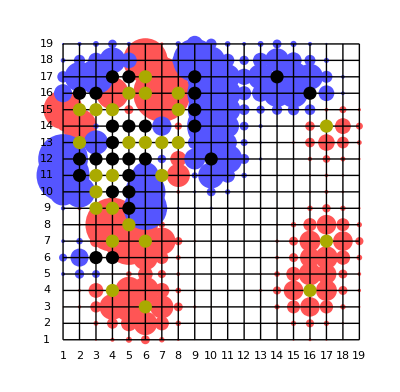

(-0.451183 | -0.932758 | -1.33914 | -1.9713 | -0.949414 | 2.285 | 0.729508 | -1.27122 | -3.71106 | -2.43836 | -1.29152 | -0.912604 | -1.35804 | -2.02575 | -1.41663 | -0.942381 | -0.480089 | -0.182995 | -0.0922557
-1.06951 | -2.54406 | -3.49229 | -5.93358 | -3.586 | 10.1129 | 2.94415 | -2.74012 | -9.87535 | -6.30436 | -3.04606 | -2.13813 | -3.47857 | -5.4948 | -3.69391 | -2.5117 | -1.182 | -0.454964 | -0.140055
-2.62116 | -6.74634 | -7.97839 | 0 | 0 | 0 | 9.12897 | 1.40834 | 0 | -10.9743 | -5.67603 | -3.70128 | -5.83017 | 0 | -6.89348 | -5.9294 | -2.7311 | -0.851556 | -0.267739
-4.11958 | 0 | 0 | 7.36232 | 0 | 0 | 13.0115 | 0 | 0 | -10.8879 | -6.04247 | -3.21148 | -3.8911 | -6.24452 | -6.57887 | 0 | -3.58875 | -0.859653 | -0.171758
8.89629 | 0 | 0 | 0 | 2.05687 | 0.482321 | 4.41856 | 0 | 0 | -10.6323 | -5.77651 | -2.46662 | -1.91244 | -2.35629 | -2.60728 | -2.43645 | 0.840486 | 1.62186 | 0.718179
2.22619 | 7.79742 | -1.25887 | 0 | 0 | 0 | -4.40365 | 1.68666 | 0 | -10.9831 | -5.17237 | -2.0234 | -0.930194 | -0.529384 | 0.355116 | 2.17981 | 0 | 3.61202 | 1.60749
1.81417 | 0 | -5.55075 | 0 | 0 | 0 | 0 | 0 | -3.0773 | -8.00011 | -4.19571 | -1.61859 | -0.59955 | -0.0811526 | 0.619191 | 2.20882 | 3.78332 | 2.68896 | 1.08808
-11.3213 | 0 | 0 | 0 | 0 | 0 | -1.94488 | 3.64978 | -4.77052 | 0 | -6.6447 | -2.29584 | -0.737939 | -0.170332 | 0.311729 | 0.979374 | 1.74469 | 1.15006 | 0.533939
-12.0799 | 0 | 0 | 0 | 0 | -6.10059 | 0 | 5.29387 | -1.40667 | -5.94248 | -3.31855 | -1.26018 | -0.471315 | -0.0722206 | 0.173109 | 0.518279 | 0.826329 | 0.578304 | 0.277014
-6.27131 | -7.14464 | 0 | 0 | 0 | -9.1492 | 1.27465 | 0.845094 | -0.678639 | -2.04393 | -1.21447 | -0.542048 | -0.205899 | 0.0107199 | 0.277014 | 0.5657 | 0.886584 | 0.578304 | 0.277014
-0.994849 | 0.91283 | 0 | 0 | 0 | -9.871 | -2.50144 | -0.667814 | -0.497869 | -0.692995 | -0.456378 | -0.205899 | -0.0107199 | 0.205899 | 0.565852 | 1.26185 | 1.91855 | 1.24576 | 0.533939
-0.308176 | 0.568384 | 4.46472 | 12.2917 | 0 | 5.75484 | 1.43673 | 0.448329 | 0.0997629 | -0.146828 | -0.0929017 | -0.0276287 | 0.147646 | 0.481793 | 1.24157 | 3.02832 | 4.48175 | 2.97205 | 1.19444
-0.855016 | -1.49235 | 2.76171 | 0 | 10.8259 | 0 | 6.21665 | 1.87749 | 0.554143 | 0.197539 | 0.0341129 | 0.0810337 | 0.285429 | 0.76994 | 2.05326 | 4.78107 | 0 | 4.48201 | 1.86562
-1.8284 | -4.11331 | 0 | 0 | -0.499783 | 5.70761 | 2.95902 | 1.09826 | 0.463383 | 0.110908 | 0.0539071 | 0.116758 | 0.306408 | 0.843339 | 2.05449 | 4.53365 | 5.17286 | 3.29144 | 1.28858
-0.897565 | -2.131 | -1.80273 | 0.460395 | 1.29837 | 3.34434 | 1.86794 | 0.864436 | 0.325362 | 0.143791 | 0.0539071 | 0.147646 | 0.487792 | 1.28858 | 3.29144 | 5.17286 | 4.53365 | 2.05449 | 0.830733
0.0614371 | 0.657099 | 3.3698 | 0 | 6.22669 | 6.21216 | 3.43737 | 1.32004 | 0.528295 | 0.172912 | 0.113932 | 0.23191 | 0.664351 | 1.86559 | 4.48082 | 0 | 4.78092 | 2.05322 | 0.76994
0.216264 | 0.755222 | 2.584 | 5.87595 | 6.71144 | 0 | 5.29809 | 2.0513 | 0.701504 | 0.246522 | 0.113932 | 0.168655 | 0.445597 | 1.19444 | 2.97094 | 4.4456 | 3.0283 | 1.24157 | 0.481793
0.119671 | 0.418052 | 1.13158 | 2.47634 | 3.62452 | 5.38895 | 3.22771 | 1.25526 | 0.466985 | 0.147646 | 0.0539071 | 0.0815358 | 0.205899 | 0.546545 | 1.19606 | 1.8585 | 1.21214 | 0.565852 | 0.205899
0.0922557 | 0.169519 | 0.465083 | 0.933634 | 1.39225 | 2.03715 | 1.25666 | 0.554756 | 0.205899 | 0.0815358 | 0 | 0 | 0.0922557 | 0.205899 | 0.445597 | 0.665652 | 0.454001 | 0.205899 | 0.0922557)

```mathematica
Board=IdentityMatrix[19]0;
whiteMoves={{16,D},{17,F},{16,P},{6,Q},{13,Q} ,{4,E},{7,E},{5,D},{5,C},
{4,F},{3,F},{5,H},{4,H},{7,H},{7,G},{9,C},{9,D},{7,B},{5,B},{10,C},
{11,D},{11,C},{9,G},{13,D},{7,F},{13,F},{12,E}};
blackMoves={{4,C}, {4,I}, {3,N},{4,P},{14,C},{10,D},{3,D},{6,E},{6,D},
{3,E},{6,F},{4,B},{5,I},{3,I},{6,I},{8,J},{7,D},{9,E},{8,B},{9,B},
{8,D},{10,E},{8,C},{8,F},{14,D},{8,E},{11,E}};
Board=ReplacePart[Board,Thread[Rule[whiteMoves/.subAlpha,1]]];
Board=ReplacePart[Board,Thread[Rule[blackMoves/.subAlpha,-1]]];

LoadBoard[Board];
brdinf=BoardInfluence;
Total@Total@brdinf
brdinf~DrawTentacles~3
brdinf//MatrixForm
```

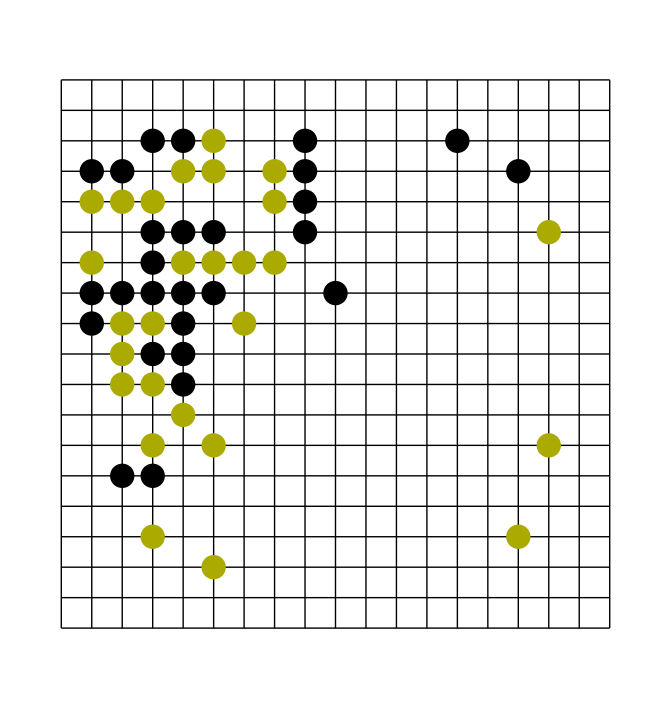

```mathematica
d = Draw[]
```

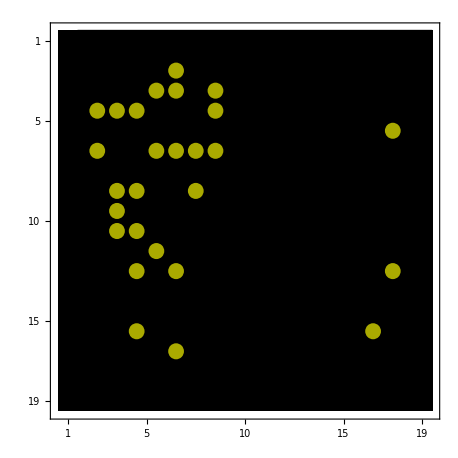

```mathematica
mp = MatrixPlot[IdentityMatrix[19] 0,PlotTheme->"Monochrome"];
Show[mp,d]
```

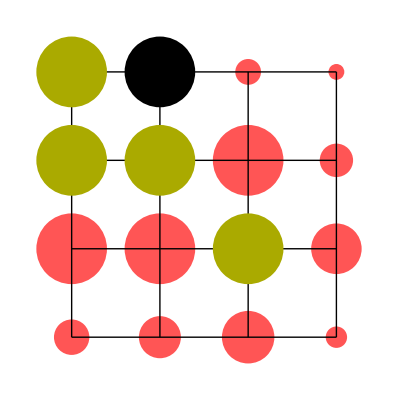

```mathematica
options={"boardPaths"-> True};
Groups[1][[1]];
{boardInf,boardPaths}= BoardInfluenceFromGroup[Groups[1][[1]],1,options];
boardInf~DrawTentacles~3
```

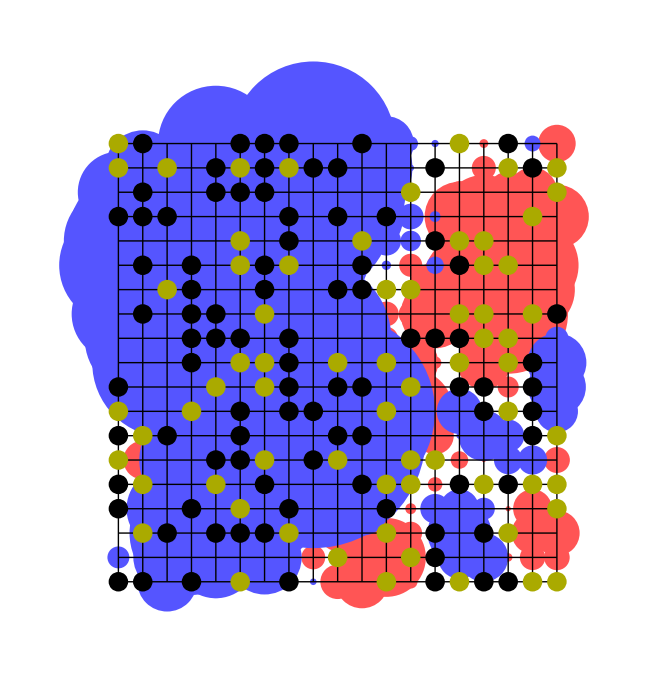

```mathematica
GenerateRandomBoard[19]
BoardInfluence~DrawTentacles~3
Draw[];
(*BoardInfluence  //RuntimeTools`Profile*)
```

```mathematica
(*Compilation attempts*)
ClearAll[AdjacentGroup,CAdjacentGroup]
AdjacentGroup[group_,coord_]:=  Intersection [{#[[1]]}&/@Position[group, Alternatives@@((coord+#)&/@listUDRL),2,4]];
CAdjacentGroup= Compile[{{group,_Integer,3},{coord,_Integer,1} },
  Intersection [{#[[1]]}&/@Flatten[Position[group,#,2,4]&/@(({2,2}+#)&/@listUDRL) ,1]]
];

Timing[AdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]
Timing[CAdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]

list[f_]:= Timing[Do[f[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}];,{#}]][[1]]&/@Range[100,2500,200]
ListPlot[{list[CAdjacentGroup],list[AdjacentGroup]} ]

<<CompiledFunctionTools`
CompilePrint[CAdjacentGroup];
```